```mathematica
(* TEXT *)
textStyle=Style[#,"Text",LineIndent->0, FontFamily->"Al Bayan"]&;

(* TIMES *)
timesStyle=Style[#,"Text",14,Bold,Blue,LineIndent->0,FontFamily->"Helvetica Neue"]&;

(* SLIDES *)
slideStyle=Style[#,"Text",Bold,Blue,LineIndent->0]&;
slide1Style=Style[#,"Text",Blue,LineIndent->0]&;

(* FORMULA *)
formulaStyle=Style[#,FontFamily->"Euclid",14]&;
formulaStyle14=Style[#,FontFamily->"Euclid",14]&;
formulaBoldStyle=Style[#,Bold,FontFamily->"Euphemia UCAS",14]&;
formulaBlueStyle=Style[#,Blue,FontFamily->"Euphemia UCAS",14]&;
```

```mathematica
(* import and parse the file containing our equations *)
SetDirectory[NotebookDirectory[]];
system =Flatten[ToExpression[StringSplit[Import["cleaned.txt", "List"], "\n"]]];
```

```mathematica
(* the demensions of the system *)
dimensions = {x1, x2, x3, x4, x5, x6, x7, x8, x9, x10, x11, x12, x13, x14, x15, x16, x17, x18, x19, x20, x21};
(* coefficents of the system *)
{B, A} = CoefficientArrays[system, dimensions];
```

```mathematica
MatrixForm[A]
```

(-556.92 | 793.76 | -833.37 | 701.23 | 253.53 | -386.79 | -272.99 | 783.53 | -800.46 | -803.43 | -421.43 | 505.17 | -951.01 | -488.34 | -697.91 | 387.42 | -103.13 | -610.66 | 659.56 | -648.07 | -337.66
170.79 | 3.01 | -915.14 | 237.16 | 190.03 | 271.77 | -852.8 | 955.09 | -49.06 | -159.33 | 915.04 | 250.8 | -219.81 | -220.42 | 19.82 | 498.58 | 384.81 | 92.45 | 930.79 | -563.66 | 898.46
389.59 | -439.76 | -571.26 | 678.09 | -587.27 | -781.37 | 73.25 | 411.69 | 167.85 | 69.54 | -273.47 | 626.66 | -610.59 | -403.16 | -448.99 | -255.71 | -525.58 | -906.89 | 671.41 | 965.49 | 414.82
711.61 | 472.24 | -540.48 | -358.79 | 736.33 | -636.51 | -886.49 | 52.58 | 357.47 | -409.87 | -798.73 | -314.61 | -916.9 | -568.76 | 205.25 | 52.23 | 759.75 | 904.78 | 190.21 | -661.14 | -16.91
149.56 | 683.41 | 317.76 | 711.77 | -210.74 | -107.38 | 154.5 | -309.28 | 975.5 | -716.48 | 943.66 | -301.14 | -732.31 | 718.86 | -987.86 | 479.33 | 396.72 | 61.29 | 668.34 | -290.25 | -865.97
972.38 | 257.51 | 746.76 | 176.63 | 911.03 | -340.43 | 600.14 | 534.84 | -315.43 | -14.93 | -488.36 | 454.47 | -120.25 | -725.65 | 462.36 | 449.15 | 981.35 | 445.9 | -113.01 | 173.78 | -67.05
-45.35 | -849.3 | -978.46 | 38.77 | -975.62 | -486.26 | 841.09 | 80.44 | 182.94 | -612.12 | -504.65 | -155.14 | 245.19 | -497.73 | 345.05 | 680.55 | -789.68 | 97.87 | -393.32 | -143.51 | 591.54
817.93 | 683.17 | 308.59 | -45.27 | -161.19 | -641.1 | 627.74 | -499.38 | -433.03 | 129.98 | 174.75 | 567.5 | -766.99 | 16.18 | 792.16 | 556.49 | -688.55 | 563.56 | -88.44 | 956.72 | -480.07
143.68 | 498.7 | 633.41 | 74.97 | -251.44 | 222.74 | 428.05 | 168.18 | -628.78 | 693.15 | 71.92 | -741.13 | 48.65 | 699.33 | 505.28 | -429.56 | -218.54 | 169.92 | 773.89 | -555.66 | -632.32
-87.55 | -472.2 | 395.02 | 864.52 | -91.61 | 610.29 | -396.72 | 114.68 | 296.18 | -277.02 | 385.43 | 471.38 | 528.72 | -96.01 | -547.41 | 39.44 | -673.84 | -950.32 | -834.42 | -855.99 | -455.14
456.19 | 15.76 | -19.23 | -42.76 | 306.25 | 8.62 | -275.73 | 195.28 | -692.14 | -951.41 | -44. | 550.33 | -49.58 | -560.22 | -793.62 | -618.4 | -908.66 | 994.44 | 11.58 | -749.4 | 493.03
-600.16 | 375.12 | -873.8 | -393.69 | -524.12 | -288.62 | -559.63 | 778.78 | 610.79 | -198.59 | -202.73 | -742.69 | 263.92 | 542.96 | -318.56 | -467.66 | -689.21 | 307.81 | -713.82 | 508.87 | 971.49
-671.3 | -107.36 | 506.68 | -489.73 | 688.09 | 256.44 | -66.1 | 223.61 | 275.39 | 14.07 | -697.83 | 364.97 | -154.93 | 797.55 | 1.22 | -532.32 | 492.23 | 286.71 | 263.25 | 963.9 | 594.99
-505.83 | -412.98 | -973.38 | -946.27 | -497.88 | 35.44 | -994.6 | 538.06 | -250.66 | 169.17 | 317.46 | -860.32 | 839.54 | 135.87 | 427.27 | -806.9 | -25.25 | 271.6 | 57.28 | -639.74 | 708.87
74.87 | -902.13 | -324.09 | -977.83 | -581.2 | 646.72 | -476.28 | -169.82 | 858.82 | -928.29 | -298.47 | 650.38 | -376.59 | -984.67 | 404.19 | 930.59 | 498.38 | -893.38 | 416.49 | -285.33 | -291.05
-524.74 | -959.57 | 591.77 | -659.44 | 789.8 | 430.72 | -854.3 | 978.32 | 117.18 | -892.68 | 605.39 | -31.29 | 430.5 | -626.01 | 104.69 | 927.08 | -191.86 | 420.02 | -617.53 | -240.52 | 89.43
-531.2 | -472.47 | 635.9 | -909.79 | -41.48 | -526.4 | 620.54 | 2.37 | 247.2 | 39.05 | -853.05 | 324.07 | -313.41 | 809.96 | -331.08 | 641.86 | -735.67 | -334.46 | 426.92 | 826.24 | -905.42
-16.13 | -46.3 | 900.99 | 205.47 | 882.27 | 267.67 | 431.94 | -386.63 | -28.79 | -565.55 | 531.08 | -633.04 | 267.22 | 726.44 | 507.76 | -939.41 | 338.02 | 384.48 | -862.2 | -473.47 | 802.86
-705.58 | -30.6 | 896.96 | 108.14 | -799.41 | 454.12 | -941.5 | 606.9 | -10.67 | 513.53 | 476.75 | -995.36 | 437.48 | -518.3 | 971.96 | 217.74 | -312.27 | 303.06 | -265.77 | -354.47 | -56.54
-871.03 | -507.31 | 890.62 | -413.69 | -373.47 | -492.65 | 438.48 | 770.97 | 566.23 | 307.77 | -663.96 | 308.48 | 557.24 | -346.25 | -294.61 | -593.74 | -361.91 | 313.78 | -108.73 | 9.05 | 944.91
817.04 | 927.76 | 688.81 | -786.28 | 954.26 | -980.58 | 300.45 | 544.42 | 127.19 | 151.73 | -704.24 | -284.73 | 369.63 | -174.42 | -38.16 | 401.12 | 869.66 | -954.64 | 38.04 | -249.98 | -956.08)

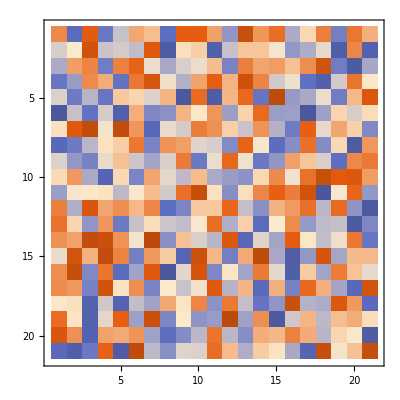

```mathematica
MatrixPlot[A,PlotTheme->"Scientific"]
```

```mathematica
ListPlot3D[A,Mesh->None,InterpolationOrder->0,ColorFunction->"SouthwestColors"]
```

```mathematica
(* -------------------------------------------------------- *)
(*    basic solution with solve                              *)
solveSolutions = Solve[system, dimensions]
```

{{x1→0.834403,x2→0.278551,x3→0.750225,x4→-0.877223,x5→-0.67107,x6→1.63143,x7→-0.151417,x8→-0.122025,x9→-0.885059,x10→0.652412,x11→-0.788524,x12→-1.31481,x13→-2.04559,x14→-0.428833,x15→-1.51564,x16→0.452994,x17→0.293732,x18→-0.711651,x19→-0.894227,x20→0.222595,x21→1.37145}}

```mathematica
(*    is nsolve the same as linear solve ? *)
nsolveSolutions = NSolve[system, dimensions];
```

```mathematica
(* -------------------------------------------------------- *)
(*    solution by matrix equation Ax=B using linearSolve      *)
```

```mathematica
linearSolutions = LinearSolve[A, -B]
```

{0.834403,0.278551,0.750225,-0.877223,-0.67107,1.63143,-0.151417,-0.122025,-0.885059,0.652412,-0.788524,-1.31481,-2.04559,-0.428833,-1.51564,0.452994,0.293732,-0.711651,-0.894227,0.222595,1.37145}

```mathematica
(* -------------------------------------------------------- *)
(*    solution using row reduce of agumented matrix *)
(*    build the augmented matrix *)
augmented=Transpose[Append[Transpose[A],-B]];
(*    row reduce the augmented matrix to find the inverse *)
reducedSolution =RowReduce[augmented];
(*    take the last column *)
reducedSolution[[All,22]]
```

{0.834403,0.278551,0.750225,-0.877223,-0.67107,1.63143,-0.151417,-0.122025,-0.885059,0.652412,-0.788524,-1.31481,-2.04559,-0.428833,-1.51564,0.452994,0.293732,-0.711651,-0.894227,0.222595,1.37145}

```mathematica
(* -------------------------------------------------------- *)
(*    solution using inverse                                 *)
inverseSolution = Inverse[A].-B
```

{0.834403,0.278551,0.750225,-0.877223,-0.67107,1.63143,-0.151417,-0.122025,-0.885059,0.652412,-0.788524,-1.31481,-2.04559,-0.428833,-1.51564,0.452994,0.293732,-0.711651,-0.894227,0.222595,1.37145}

```mathematica
(* -------------------------------------------------------- *)
(*    solution using craimers rule                           *)
(*    craimers rule module from rosettacode.com *)
crule[m_,b_]:=Module[
{d=Det[m],a},
Table[
a=m;
a[[All,k]]=b;
Det[a]/d,
{k,Length[m]}
]
]
crule[A, -B]
```

{0.834403,0.278551,0.750225,-0.877223,-0.67107,1.63143,-0.151417,-0.122025,-0.885059,0.652412,-0.788524,-1.31481,-2.04559,-0.428833,-1.51564,0.452994,0.293732,-0.711651,-0.894227,0.222595,1.37145}

```mathematica
f[x_] := system[1]
```

```mathematica
s = Solve
```